```mathematica
Off[General::spell1]
```

```mathematica
face::usage = "face[{headecc_, eyesize_, eyespacing_, 
		eyeeccent_, pupsize_, browslant_, nozesize_,
		mouthshape_, mouthsize_, mouthopening_}]";
```

```mathematica
face[{headecc_, eyesize_, eyespacing_, eyeeccent_, 
	  pupsize_, browslant_, nozesize_, mouthshape_,
	  mouthsize_, mouthopening_}] :=
    Graphics[Flatten[
       {head[headecc],
        eyes[eyesize, eyespacing, eyeeccent, 
        	 pupsize],
        brows[browslant], nose[nozesize],
        mouth[mouthshape, mouthsize, mouthopening]}], 
                    AspectRatio -> Automatic,  
                    PlotRange-> {{-1.5, 1.5}, 
                    			 {-1.5, 1.5}}]
```

```mathematica
head[eccent_] := 
Block[
{xrad = 1 + (eccent - 5) / 25,
yrad = 1 - (eccent - 5) / 25},
Circle[{0, 0}, (1 + Abs[eccent - 5]/20){xrad, yrad}]
]
```

```mathematica
eyes[size_, spacing_, eccent_, pupsize_] :=
Block[
{xcenter = (1/3) + (spacing - 5) / 30,xrad = (1/6) + ((size - 5) + (eccent - 5))/70,
         yrad = (1/6) + ((size - 5) - (eccent - 5))/70},
  {Circle[{xcenter, 1/3},  {xrad, yrad}],
    PointSize[(pupsize + 1) / 200], 
    Point[{xcenter, 1/3}],
    Circle[{-xcenter, 1/3},  {xrad, yrad}],
    PointSize[(pupsize + 1) / 200], 
    Point[{-xcenter, 1/3}]}
]
```

```mathematica
brows[slant_] :=  Block[
       {xstart = (1/3) - (1/6) Cos[(slant - 5) Pi 
       							    / 20],
        ystart = (2/3) - (1/6) Sin[(slant - 5) Pi 
        							/ 20],
        xend = (1/3) + (1/6) Cos[(slant - 5) Pi 
        						  / 20],
        yend =  (2/3) + (1/6) Sin[(slant - 5) Pi 
        						   / 20]},
    {Line[{{xstart, ystart}, {xend, yend}}],
     Line[{{-xstart, ystart}, {-xend, yend}}]}
]
```

```mathematica
nose[size_] := Block[
        {scale = 1 + (size - 5) / 13},
 Line[scale {{0, 1/6}, {-1/6, -1/6}, 
 			 {1/6, -1/6}, {0, 1/6}}]
]
```

```mathematica
mouth[shape_, size_, opening_] := Block[
  {fx, gx, xstart, xend, ystart, ymin, ymax, xstep },
 xstart = -1/3 - (size - 5) / 15; 
 xend = 1/3 + (size - 5) / 15;
 ystart = -1/2 + (shape - 5) * size / 150;
 ymax = -1/2 + (.9 opening - 1) / 27;
 ymin = -1/2 - (.9 opening - 1) / 30;
 fx = Fit[{{xstart, ystart}, {0, ymax}, 
 		   {xend, ystart}}, {1, x, x^2}, x];
 gx = Fit[{{xstart, ystart}, {0, ymin},
 		   {xend, ystart}}, {1, x, x^2}, x];
 xstep = (xend - xstart) / 10;
    {Line[Table[{x, fx}, {x, xstart, xend, xstep}]],
     Line[Table[{x, gx}, {x, xstart, xend, xstep}]]}
]
```

```mathematica
On[General::spell1]
```

```mathematica
ClearAll[data27]
data27=Table[Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2015\\April\\27\\27apr_"<>ToString[i]<>"ac.dat"],{i,1,7}];
```

```mathematica
amplitude=Table[data27[[i]][[All,2]]*data27[[6]][[1,2]]/data27[[i]][[1,2]],{i,1,7}];
```

```mathematica
nonLogorifmicTime = 
  Table[Transpose[{data27[[i]][[All, 3]]-1.68, amplitude[[i]]}], {i, 
    1, 7}];
```

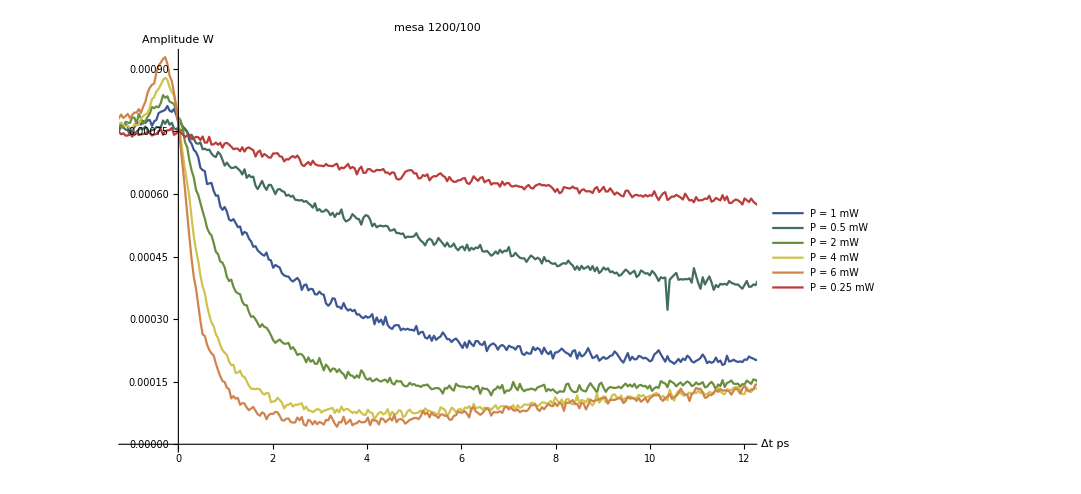

```mathematica
ListLinePlot[Table[nonLogorifmicTime[[i]],{i,1,6}],PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW","P = 0.25 mW"},ImageSize->800,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{-1,12},All},PlotStyle->"DarkRainbow"]
```

```mathematica
forFit=Table[MeanFilter[nonLogorifmicTime[[i]],{5,0}][[37;;300;;15]],{i,1,6}];
```

```mathematica
steps = forFit[[3]][[;;,1]];
```

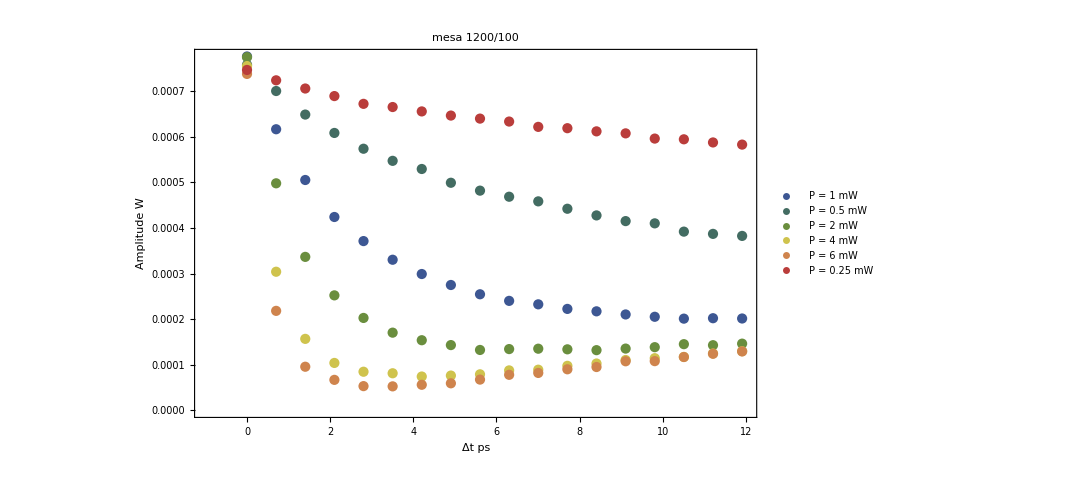

```mathematica
ListPlot[Table[forFit[[i]],{i,1,6}],PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW","P = 0.25 mW"},ImageSize->800,PlotLabel->"mesa 1200/100",Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{-1,12},All},PlotStyle->"DarkRainbow"]
```

```mathematica
w=Table[3.3*(i/.5)^(1/2),{i,{.25,.5,1,2,4,6}}]
```

{2.33345,3.3,4.6669,6.6,9.33381,11.4315}

```mathematica
Manipulate[
solIn=NDSolve[{p''[x]+a*p'[x]+a*r*p[x]+(w[[1]])^2/n*p[x]*Exp[-x*c]==10^3*(w[[1]])^2*e*Exp[-x*c], p[0]==0, p'[0]==0},  p[x],{x,0, 12}];
Show[ListPlot[forFit[[1]]],Plot[(1-p[x]/n/e/10^3)/forFit[[1]][[1,2]]^-1 /. solIn, {x,0,12},PlotRange->All],PlotRange->All],
{{a,14.}, 1,20}, {{c,0.762},0.1,1.2}, {{n,3.38},0.1,3.5},{{e,3.22},1,20}, {{r,0.010623}, 0, 0.015}]
```

```mathematica
Manipulate[
dat=Table[
Total[
(forFit[[j]][[1,2]]
-NDSolveValue[{p''[x]+a*p'[x]+a*r*p[x]+w[[j]]^2/n*p[x]*Exp[-x*c]==10^3*w[[j]]^2*e*Exp[-x*c], p[0]==0, p'[0]==0},  p,{x,0,12}]/@steps/n/e/10^3/forFit[[j]][[1,2]]^(-1)-forFit[[j]][[All,2]])^2],
{j,1,6}];
Column[{
Row[
{a," ",c," ",n," ",e," ",r}
],
Grid[
{{Column[dat],
face[{dat[[1]]*10^6, dat[[2]]*10^6, dat[[3]]*10^6, dat[[4]]*10^6, dat[[5]]*10^6, dat[[6]]*10^6, 5, 5, 5, 5}],
face[{0,0,0,0,0,0,5,5,5,5}]}}
]
}
,Center],
{{a,10.}, 1,30}, {{c,0.762},0.1,4}, {{n,3.38},0.1,5},{{e,3.22},1,20}, {{r,0.010623}, 10^-6, 0.02}
]
```